{0.326797-0.945094 ⅈ,0.945094+0.326797 ⅈ,0.+0. ⅈ}

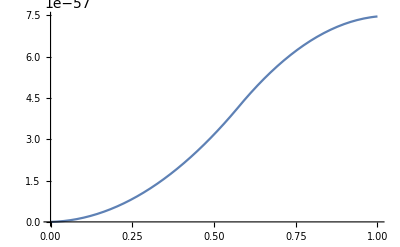

```mathematica
(* Define constants *)
SiteNum =2; (* Total site number *)
Subscript[U, 0]=10/1000×(1.6×10^-19);(* Coulomb interaction strength *)
Subscript[a, 0]=1.0;(* spatial cutoff *)
Subscript[d, 0]=2 Subscript[a, 0];(* lattice constant *)
Subscript[μ, 0]=10^-3;(* electric dipole *)
Subscript[τ, ex]=10000×10^-15;(* dephasing time *)
τ=1000×10^-15;(* pulse centered at τ *)

Subscript[ω, α]=3.62/1000×(1.6×10^-19)/(6.626×10^-34)/(2Pi);(* carrier detune frequency *)
Subscript[ω, g]=1.5×(1.6×10^-19)/(6.626×10^-34)/(2Pi);
Subscript[δ, α]=100×10^-15;
tmax=100×10^-12;(* simulation time *)

x̂={1,0,0};
ŷ={0,1,0};
ẑ={0,0,1};


ê=x̂+I ŷ;
(* external field *)
Eex[t_,τ_,δ_]:=
(*{0,0,0}*)
ê Exp[-(t-τ)^2/δ^2]Exp[-I (Subscript[ω, α]+Subscript[ω, g])t];


(* Define T matrix *)
Subscript[T, v][i_,j_,v_]:=
If[i==j,0.5*1.5×(1.6×10^-19),
If[Abs[v]==3/2,4.75/1000×(1.6×10^-19),2.52/1000×(1.6×10^-19)]
] (* valence band *)

Subscript[T, c][i_,j_,c_]:=
If[i==j,0.5*1.5×(1.6×10^-19),8/1000×(1.6×10^-19)](* conduction band *)


(* Define Coulomb potential *)
V[i_,j_]:=
Subscript[U, 0] Subscript[d, 0]/(Subscript[a, 0]+Subscript[d, 0] Abs[i-j])


(* Define electirc dipole *)
μ[i_,j_,s_,r_]:=
If[i≠j,{0,0,0},If[s-r==-1,Subscript[μ, 0](x̂+I ŷ),Subscript[μ, 0](x̂-I ŷ),Subscript[μ, 0]]]


(* Generate equations *)
write[i_,j_,s_,r_,t_]:=
-ⅈ Subscript[p, i,j,s,r]'[t]-ⅈ/Subscript[τ, ex]  Subscript[p, i,j,s,r][t]== -∑_(n=1)^SiteNum Subscript[T, c][j,n,r] Subscript[p, i,n,s,r][t] -∑_(n=1)^SiteNum Subscript[T, v][i,n,s] Subscript[p, n,j,s,r][t] +V[i,j] Subscript[p, i,j,s,r][t]+ Eex[t,τ,Subscript[δ, α]].μ[i,j,s,r]* 


(* Generate initial conditions *)
write2[i_,j_,s_,r_,t_]:=
Subscript[p, i,j,s,r][0]==0


(* Generate list of unknows *)
write3[i_,j_,s_,r_,t_]:=
Subscript[p, i,j,s,r][t]


(* Final expressions *)
equations={};
initial={};
Unknowns={};
subscript={};
For[i=1,i≤ SiteNum,i++,
For[j = 1,j≤SiteNum,j++,
For[s=-3/2,s≤3/2,s++,
If[s==-3/2,r=-1/2;AppendTo[equations,write[i,j,s,r,t]];AppendTo[initial,write2[i,j,s,r,t]];AppendTo[Unknowns,write3[i,j,s,r,t]];
AppendTo[subscript,{i,j,s,r}]
];
If[s==-1/2,r=+1/2;AppendTo[equations,write[i,j,s,r,t]];AppendTo[initial,write2[i,j,s,r,t]];AppendTo[Unknowns,write3[i,j,s,r,t]];
AppendTo[subscript,{i,j,s,r}]
];
If[s==+1/2,r=-1/2;AppendTo[equations,write[i,j,s,r,t]];AppendTo[initial,write2[i,j,s,r,t]];AppendTo[Unknowns,write3[i,j,s,r,t]];
AppendTo[subscript,{i,j,s,r}]
];
If[s==+3/2,r=+1/2;AppendTo[equations,write[i,j,s,r,t]];AppendTo[initial,write2[i,j,s,r,t]];AppendTo[Unknowns,write3[i,j,s,r,t]];
AppendTo[subscript,{i,j,s,r}]
];
]
]
]


(* Solve ode *)
sol = Unknowns/.
NDSolve[Join[equations,initial],Unknowns,{t,0,tmax}];

(* Interband polarization *)
P=0.0;
For[n=1,n≤4 SiteNum^2,n++,p[n] =sol[[1]][[n]];P=P+2Re[μ[subscript[[n]][[1]],subscript[[n]][[2]],subscript[[n]][[3]],subscript[[n]][[4]]] p[n]]] ;(* p[n] = p_{subscript[[n]]}*)
Plot[{Norm[P],Norm[Eex[t]]/norm},{t,0,tmax/10}]
```

```mathematica
norm=(Norm[P]/.(t->τ))
```

1.50325×10^-58

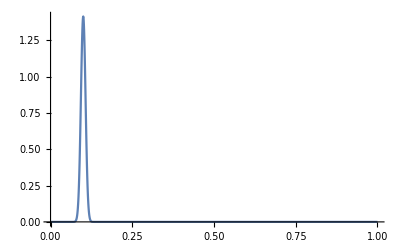

```mathematica
Plot[{Norm[Eex[t,τ,Subscript[δ, α]]]},{t,0,tmax/10},PlotRange->All]
```